```mathematica
description="Slepton counterterms";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

## LO diagrams to combine for interference terms

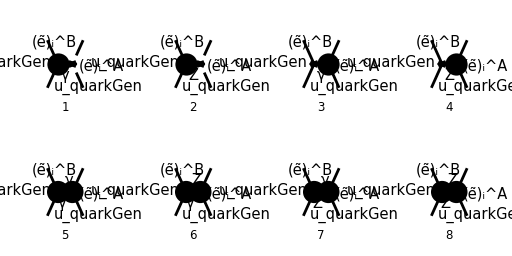

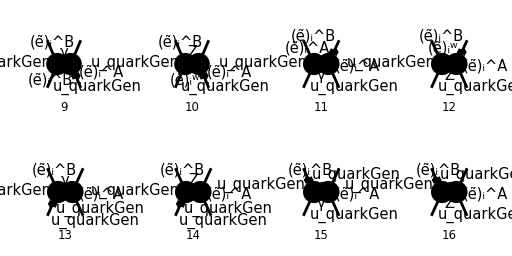

```mathematica
diagsCT[0]=InsertFields[
CreateCTTopologies[1,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSMCT,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4]}
];
Paint[
diagsCT[0],
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

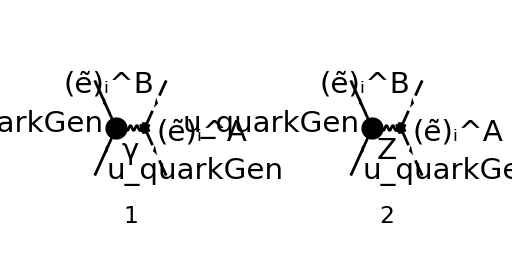

```mathematica
diagsCT[1]=DiagramExtract[diagsCT[0],{1,2}];
Paint[
diagsCT[1],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
MCTlist[0]=FCFAConvert[
CreateFeynAmp[diagsCT[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
Contract->True,
DropSumOver->True,
SMP->True,
List->True
]/.{MQU[quarkGen]->0}
```

{(e^2 δ_Col1Col2 (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) (dZZA1 ((1-2 (sin(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]-2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))])+2 (cos(θ_W)) (sin(θ_W)) ((dZAA1+2 dZe1) IndexDelta(A,B)+IndexDelta(1,B) dZbarSf1(1,A,2,i)+IndexDelta(2,B) dZbarSf1(2,A,2,i)+IndexDelta(1,A) dZSf1(1,B,2,i)+IndexDelta(2,A) dZSf1(2,B,2,i))))/(6 (cos(θ_W)) (sin(θ_W)) (k_1+k_2)^2),(ⅈ e (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-(sin(θ_W)) (2 (sin(θ_W)) Conjugate[(USf(2,i)(B,2))] (USf(2,i)(A,2) ((cos(θ_W))^2 (2 dSW1+(2 dZe1+dZZZ1) (sin(θ_W)))+2 dSW1 (sin(θ_W))^2)+(cos(θ_W))^2 (sin(θ_W)) (USf(2,i)(1,2) dZbarSf1(1,A,2,i)+USf(2,i)(2,2) dZbarSf1(2,A,2,i)))+(cos(θ_W))^2 ((1-2 (cos(θ_W))^2) USf(2,i)(A,1) (dZSf1(1,B,2,i) Conjugate[(USf(2,i)(1,1))]+dZSf1(2,B,2,i) Conjugate[(USf(2,i)(2,1))])+2 (sin(θ_W))^2 USf(2,i)(A,2) (dZSf1(1,B,2,i) Conjugate[(USf(2,i)(1,2))]+dZSf1(2,B,2,i) Conjugate[(USf(2,i)(2,2))])))-Conjugate[(USf(2,i)(B,1))] (USf(2,i)(A,1) ((cos(θ_W))^2 (dSW1 (6-4 (cos(θ_W))^2)+(2 dZe1+dZZZ1) (1-2 (cos(θ_W))^2) (sin(θ_W)))-dSW1 (2 (sin(θ_W))^2-4 (sin(θ_W))^4))+(1-2 (cos(θ_W))^2) (cos(θ_W))^2 (sin(θ_W)) (USf(2,i)(1,1) dZbarSf1(1,A,2,i)+USf(2,i)(2,1) dZbarSf1(2,A,2,i)))+2 dZAZ1 (cos(θ_W))^3 (sin(θ_W))^2 IndexDelta(A,B)))/(4 (cos(θ_W))^3 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))}

```mathematica
MCTγ[0]=MCTlist[0][[1]]
```

(e^2 δ_Col1Col2 (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) (dZZA1 ((1-2 (sin(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]-2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))])+2 (cos(θ_W)) (sin(θ_W)) ((dZAA1+2 dZe1) IndexDelta(A,B)+IndexDelta(1,B) dZbarSf1(1,A,2,i)+IndexDelta(2,B) dZbarSf1(2,A,2,i)+IndexDelta(1,A) dZSf1(1,B,2,i)+IndexDelta(2,A) dZSf1(2,B,2,i))))/(6 (cos(θ_W)) (sin(θ_W)) (k_1+k_2)^2)

```mathematica
MCTγ[1]=MCTγ[0]//ZSimplify
```

(e^2 δ_Col1Col2 (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) (dZZA1 USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 dZAA1 (cos(θ_W)) (sin(θ_W)) IndexDelta(A,B)+2 IndexDelta(1,B) (cos(θ_W)) (sin(θ_W)) dZbarSf1(1,A,2,i)+2 IndexDelta(2,B) (cos(θ_W)) (sin(θ_W)) dZbarSf1(2,A,2,i)+4 dZe1 (cos(θ_W)) (sin(θ_W)) IndexDelta(A,B)+2 IndexDelta(1,A) (cos(θ_W)) (sin(θ_W)) dZSf1(1,B,2,i)+2 IndexDelta(2,A) (cos(θ_W)) (sin(θ_W)) dZSf1(2,B,2,i)-2 dZZA1 (sin(θ_W))^2 A,B))/(6 (cos(θ_W)) (sin(θ_W)) (k_1+k_2)^2)